```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210507_time_windows_and_OR_model"];
```

Data Import_Fixed Boundaries

```mathematica
modularityvalues12m4p4=Import["plot_values/(-4,4)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/(-1,1)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/(-2,-4)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/(2,4)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/(-4,4)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/(-1,1)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/(-2,-4)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/(2,4)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/(-4,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/(-4,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/(-1,1)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/(-1,1)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/(-2,-4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/(-2,-4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/(2,4)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/(-4,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/(-4,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/(-1,1)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/(-1,1)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/(-2,-4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/(-2,-4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/(2,4)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/(-4,4)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/(-1,1)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/(-2,-4)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/(2,4)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/(-4,4)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/(-1,1)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/(-2,-4)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/(2,4)-zscores-fbs.mx"];
```

```mathematica
win2=37;
```

```mathematica
modularityvalues12={Thread[{Range@win2,modularityvalues12m4p4}],Thread[{Range@win2,modularityvalues12m1p1}],Thread[{Range@win2,modularityvalues12m2m4}],Thread[{Range@win2,modularityvalues12p2p4}]};
modularityvalues32={Thread[{Range@win2,modularityvalues32m4p4}],Thread[{Range@win2,modularityvalues32m1p1}],Thread[{Range@win2,modularityvalues32m2m4}],Thread[{Range@win2,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{Range@win2,singlerandomerdrenmodularityvalues12m4p4}],Thread[{Range@win2,singlerandomcommmodularityvalues12m4p4}],Thread[{Range@win2,singlerandomerdrenmodularityvalues12m1p1}],Thread[{Range@win2,singlerandomcommmodularityvalues12m1p1}],Thread[{Range@win2,singlerandomerdrenmodularityvalues12m2m4}],Thread[{Range@win2,singlerandomcommmodularityvalues12m2m4}],Thread[{Range@win2,singlerandomerdrenmodularityvalues12p2p4}],Thread[{Range@win2,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{Range@win2,singlerandomerdrenmodularityvalues32m4p4}],Thread[{Range@win2,singlerandomcommmodularityvalues32m4p4}],Thread[{Range@win2,singlerandomerdrenmodularityvalues32m1p1}],Thread[{Range@win2,singlerandomcommmodularityvalues32m1p1}],Thread[{Range@win2,singlerandomerdrenmodularityvalues32m2m4}],Thread[{Range@win2,singlerandomcommmodularityvalues32m2m4}],Thread[{Range@win2,singlerandomerdrenmodularityvalues32p2p4}],Thread[{Range@win2,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{Range@win2,zscores12m4p4[[All,1]]}],Thread[{Range@win2,zscores12m4p4[[All,2]]}],Thread[{Range@win2,zscores12m1p1[[All,1]]}],Thread[{Range@win2,zscores12m1p1[[All,2]]}],Thread[{Range@win2,zscores12m2m4[[All,1]]}],Thread[{Range@win2,zscores12m2m4[[All,2]]}],Thread[{Range@win2,zscores12p2p4[[All,1]]}],Thread[{Range@win2,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{Range@win2,zscores32m4p4[[All,1]]}],Thread[{Range@win2,zscores32m4p4[[All,2]]}],Thread[{Range@win2,zscores32m1p1[[All,1]]}],Thread[{Range@win2,zscores32m1p1[[All,2]]}],Thread[{Range@win2,zscores32m2m4[[All,1]]}],Thread[{Range@win2,zscores32m2m4[[All,2]]}],Thread[{Range@win2,zscores32p2p4[[All,1]]}],Thread[{Range@win2,zscores32p2p4[[All,2]]}]};
```

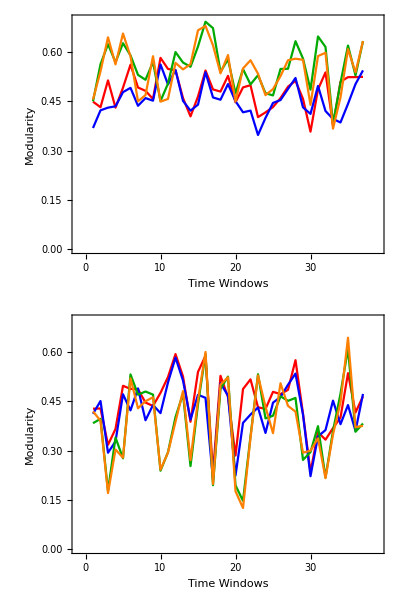
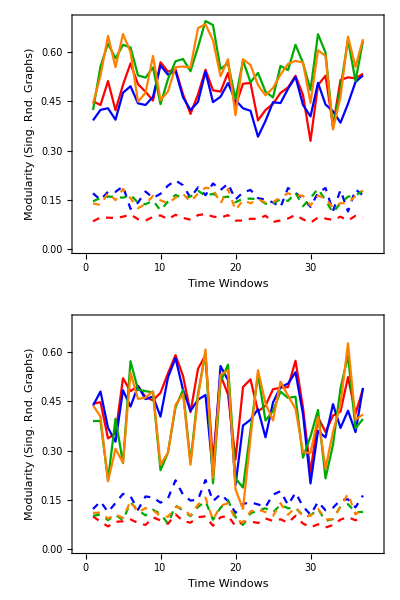
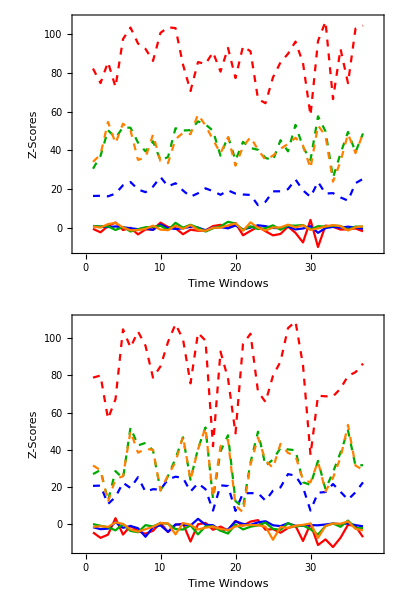

```mathematica
padding=38;
modularityplotrange={0,0.7};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Time Windows",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Time Windows",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[{zscores12m1p1,zscores12m2m4,zscores12m4p4,zscores12p2p4}],1]}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[{zscores32m1p1,zscores32m2m4,zscores32m4p4,zscores32p2p4}],1]}]}]
,Column[{LineLegend[{Darker@Green,Blue,Orange,Red},{"[-4,-2]","[-1,1]","[2,4]","[-4,4]"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Objective Function\nCoefficient Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

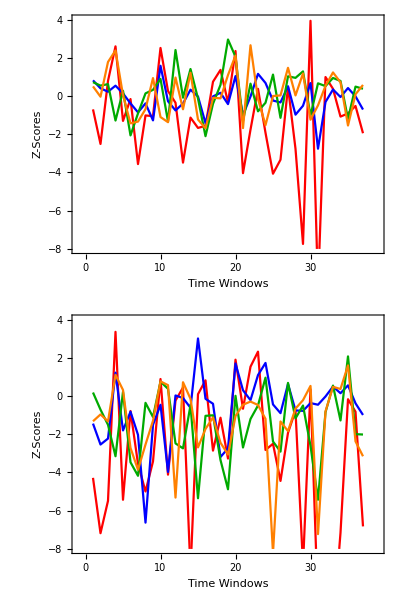

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},{-8,4}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},{-8,4}}]}]
```

Data Import_Fixed Objective Function Coefficients

```mathematica
modularityvalues12m4p4=Import["plot_values/boundaries_(-0.5,0.5)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/boundaries_(-50,50)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/boundariesdouble_(-0.5,0.5)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/boundariesdouble_(-50,50)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/boundaries_(-0.5,0.5)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/boundaries_(-50,50)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/boundariesdouble_(-0.5,0.5)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/boundariesdouble_(-50,50)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/boundaries_(-0.5,0.5)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/boundaries_(-0.5,0.5)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/boundaries_(-50,50)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/boundaries_(-50,50)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/boundariesdouble_(-0.5,0.5)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/boundariesdouble_(-0.5,0.5)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/boundariesdouble_(-50,50)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/boundariesdouble_(-50,50)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/boundaries_(-0.5,0.5)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/boundaries_(-0.5,0.5)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/boundaries_(-50,50)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/boundaries_(-50,50)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/boundariesdouble_(-0.5,0.5)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/boundariesdouble_(-0.5,0.5)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/boundariesdouble_(-50,50)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/boundariesdouble_(-50,50)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/boundaries_(-0.5,0.5)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/boundaries_(-50,50)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/boundariesdouble_(-0.5,0.5)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/boundariesdouble_(-50,50)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/boundaries_(-0.5,0.5)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/boundaries_(-50,50)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/boundariesdouble_(-0.5,0.5)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/boundariesdouble_(-50,50)-zscores-fbs.mx"];
```

```mathematica
win2=37;
```

```mathematica
modularityvalues12={Thread[{Range@win2,modularityvalues12m4p4}],Thread[{Range@win2,modularityvalues12m1p1}],Thread[{Range@win2,modularityvalues12m2m4}],Thread[{Range@win2,modularityvalues12p2p4}]};
modularityvalues32={Thread[{Range@win2,modularityvalues32m4p4}],Thread[{Range@win2,modularityvalues32m1p1}],Thread[{Range@win2,modularityvalues32m2m4}],Thread[{Range@win2,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{Range@win2,singlerandomerdrenmodularityvalues12m4p4}],Thread[{Range@win2,singlerandomcommmodularityvalues12m4p4}],Thread[{Range@win2,singlerandomerdrenmodularityvalues12m1p1}],Thread[{Range@win2,singlerandomcommmodularityvalues12m1p1}],Thread[{Range@win2,singlerandomerdrenmodularityvalues12m2m4}],Thread[{Range@win2,singlerandomcommmodularityvalues12m2m4}],Thread[{Range@win2,singlerandomerdrenmodularityvalues12p2p4}],Thread[{Range@win2,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{Range@win2,singlerandomerdrenmodularityvalues32m4p4}],Thread[{Range@win2,singlerandomcommmodularityvalues32m4p4}],Thread[{Range@win2,singlerandomerdrenmodularityvalues32m1p1}],Thread[{Range@win2,singlerandomcommmodularityvalues32m1p1}],Thread[{Range@win2,singlerandomerdrenmodularityvalues32m2m4}],Thread[{Range@win2,singlerandomcommmodularityvalues32m2m4}],Thread[{Range@win2,singlerandomerdrenmodularityvalues32p2p4}],Thread[{Range@win2,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{Range@win2,zscores12m4p4[[All,1]]}],Thread[{Range@win2,zscores12m4p4[[All,2]]}],Thread[{Range@win2,zscores12m1p1[[All,1]]}],Thread[{Range@win2,zscores12m1p1[[All,2]]}],Thread[{Range@win2,zscores12m2m4[[All,1]]}],Thread[{Range@win2,zscores12m2m4[[All,2]]}],Thread[{Range@win2,zscores12p2p4[[All,1]]}],Thread[{Range@win2,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{Range@win2,zscores32m4p4[[All,1]]}],Thread[{Range@win2,zscores32m4p4[[All,2]]}],Thread[{Range@win2,zscores32m1p1[[All,1]]}],Thread[{Range@win2,zscores32m1p1[[All,2]]}],Thread[{Range@win2,zscores32m2m4[[All,1]]}],Thread[{Range@win2,zscores32m2m4[[All,2]]}],Thread[{Range@win2,zscores32p2p4[[All,1]]}],Thread[{Range@win2,zscores32p2p4[[All,2]]}]};
```

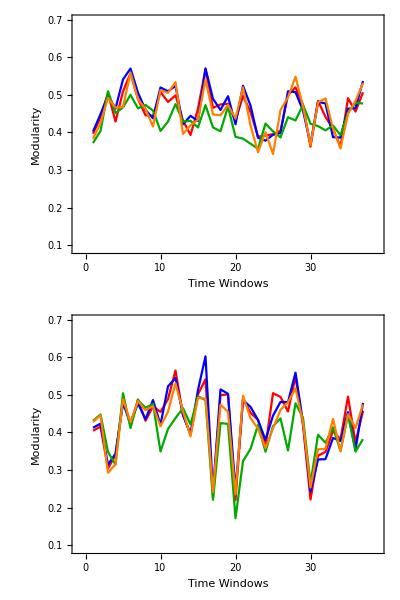
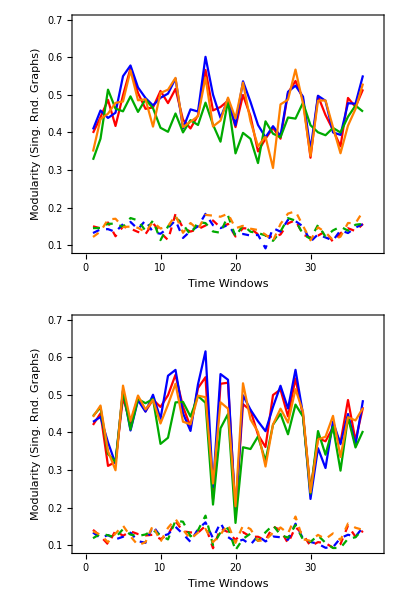
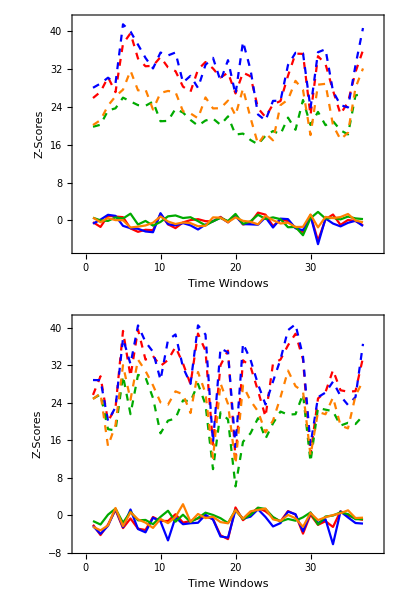

```mathematica
padding=38;
modularityplotrange={0.09,0.7};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Time Windows",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Time Windows",None}},PlotStyle->{Red,Blue,Darker@Green,Orange},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[{zscores12m1p1,zscores12m2m4,zscores12m4p4,zscores12p2p4}],1]}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[{zscores32m1p1,zscores32m2m4,zscores32m4p4,zscores32p2p4}],1]}]}]
,Column[{LineLegend[{Red,Darker@Green,Blue,Orange},{"[-0.5,0.5] -> 105pcs","[-0.5,0.5] -> 210pcs","[-50,50] -> 105pcs","[-50,50] -> 210pcs"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Constrained\nBound Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

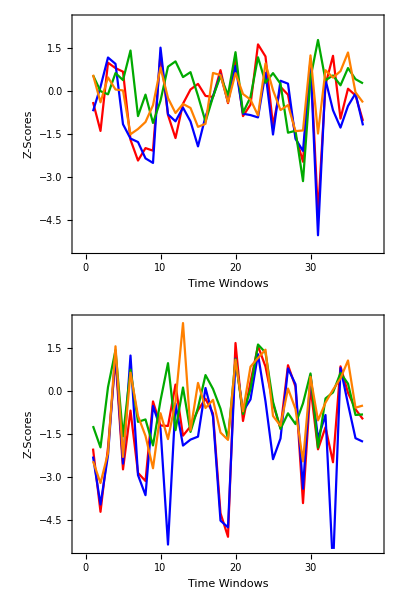

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},{-5.5,2.5}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Time Windows",None}},PlotStyle->{{Dashed,Red},Red,{Dashed,Blue},Blue,{Dashed,Darker@Green},Darker@Green,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{{-1,win2+2},{-5.5,2.5}}]}]
```